```mathematica
Get[FileNameJoin[{NotebookDirectory[], "PositUtils.m"}]]
```

```mathematica
setpositenv[{3,1}]
{nbits,es,npat,useed,minpos,maxpos,qsize,qextra}
x2p[ComplexInfinity]
```

{3,1,8,4,1/4,4,16,8}

4

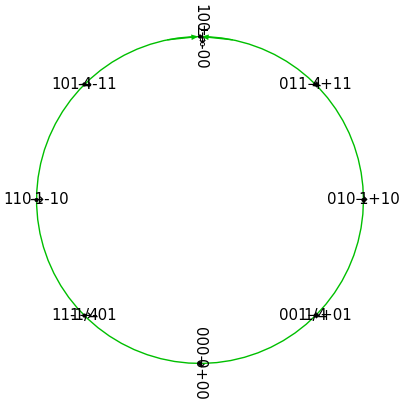

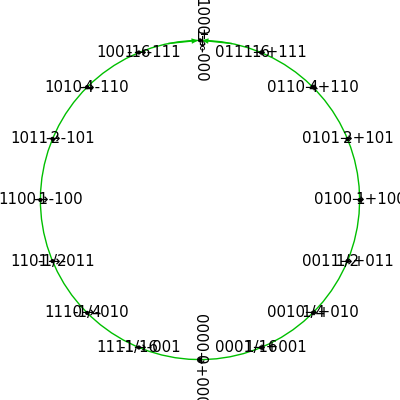

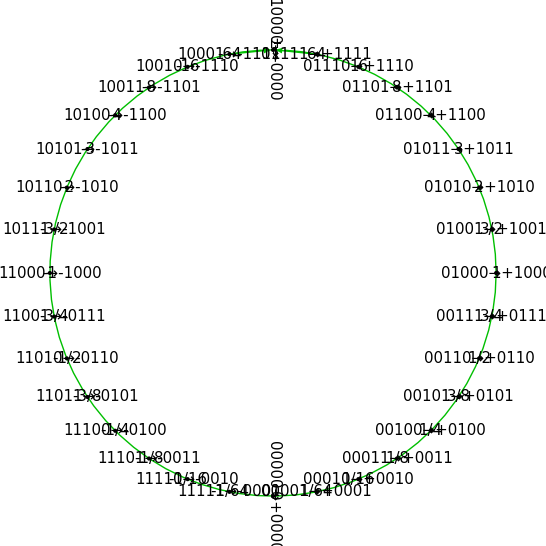

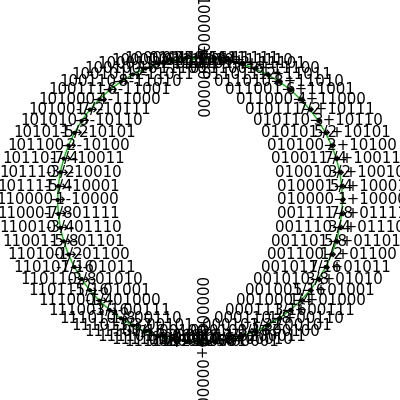

```mathematica
Get[FileNameJoin[{NotebookDirectory[], "PositUtils.m"}]]
setpositenv[{3,1}];ringplot
setpositenv[{4,1}];ringplot
setpositenv[{5,1}];ringplot
setpositenv[{6,1}];ringplot
```

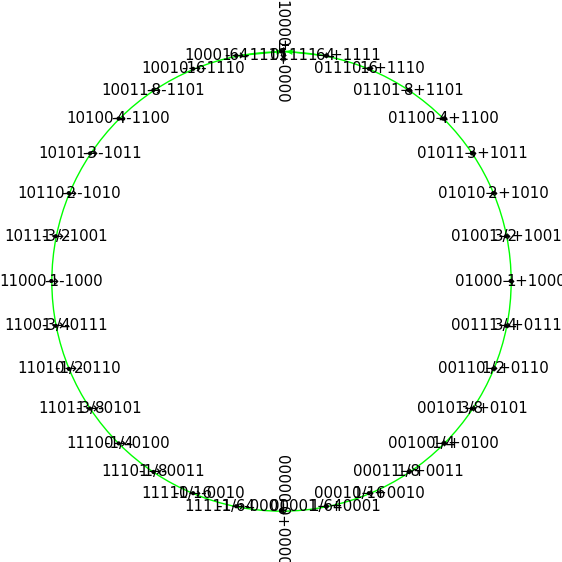

```mathematica
setpositenv[{5,1}];
nums=
Table[Row[{Style[p2x[j]//InputForm, Purple]}],
{j,0,npat-1}];
nums[[x2p[ComplexInfinity]+1]]=
Row[{Style["±∞", Purple]}];
bits=
Table[Row[{Style[colorcodep[j], FontFamily->"Courier", FontWeight->Bold]}],
{j,0,npat-1}];
posits=Table[Row[{Style[p2x[j]//InputForm, Purple],"      ",Style[colorcodep[j], FontFamily->"Courier", FontWeight->Bold]}],
{j,0,npat-1}];
posits[[x2p[ComplexInfinity]+1]]=Row[{Style["±∞", Purple],"      ",Style[colorcodep[x2p[ComplexInfinity]], FontFamily->"Courier", FontWeight->Bold]}];
Graphics[{Green,Thick,Circle[],{Arrowheads[0.06],Arrow[{{0.2,0.98},{0.02,1}}]},{Arrowheads[0.06],Arrow[{{-0.2,0.98},{0.01,1}}]},Black,PointSize[Large],Point[c=CirclePoints[{1,-Pi/2},npat]],
(*Table[Text[Style[posits[[i]],15],
			c[[i]],Scaled[{0.3,.5}],c[[i]]],{i,npat}]*)
Table[{
Text[Style[nums[[i]],15],c[[i]],Scaled[{2/(StringLength[ToString[nums[[i]]]]^0.35),.5}],c[[i]]], Text[Style[bits[[i]],15],c[[i]],Scaled[{-.1,.5}],c[[i]]],Text[Style[nums[[npat-i+1]],15],c[[-i]],Scaled[{-1/StringLength[ToString[nums[[npat-i+1]]]],.5}],-c[[-i]]],
Text[Style[bits[[npat-i+1]],15],c[[-i]],Scaled[{1.1,.5}],-c[[-i]]]
},{i,npat/2}]
}]
```

```mathematica
StringLength[ToString[nums[[npat]]]]
```

5

```mathematica
ringplot:=(
posits=Table[Row[{Style[p2x[j], Purple],"      ",Style[colorcodep[j], FontFamily->"Courier", FontWeight->Bold]}],
{j,0,npat-1}];
posits[[x2p[ComplexInfinity]+1]]=Row[{Style["±∞", Purple],"      ",Style[colorcodep[x2p[ComplexInfinity]], FontFamily->"Courier", FontWeight->Bold]}];
Graphics[{Green,Thick,Circle[],{Arrowheads[0.06],Arrow[{{0.2,0.98},{0.02,1}}]},{Arrowheads[0.06],Arrow[{{-0.2,0.98},{0.01,1}}]},Black,PointSize[Large],Point[c=CirclePoints[{1,-Pi/2},npat]],Table[Text[Style[StringRepeat[" ",4*nbits]posits[[i]],15],c[[i]],Automatic,c[[i]]],{i,npat}]}])
```

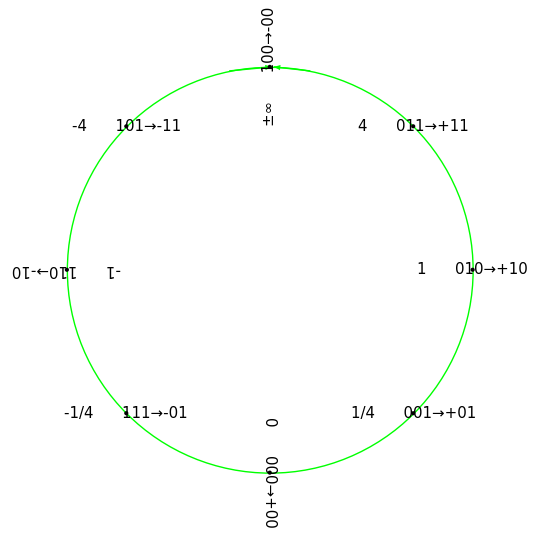

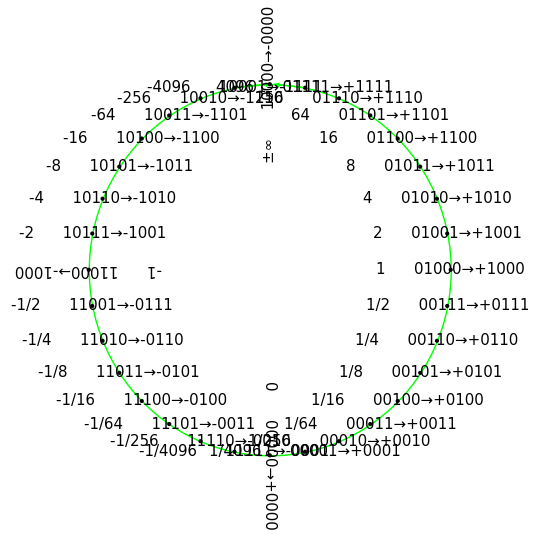

```mathematica
setpositenv[{3,1}];ringplot
setpositenv[{5,2}];ringplot
```

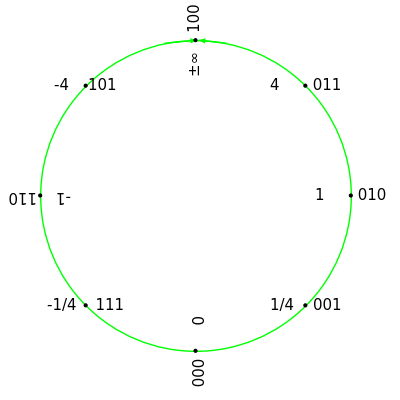

```mathematica
t1=""<>ToString/@#&/@Tuples[{0,1},3];
t2={"0   ","1/4","1   ","4   ","±∞","-4","-1","-1/4"};
Graphics[{Green,Thick,Circle[],{Arrowheads[0.06],Arrow[{{0.2,0.98},{0.02,1}}]},{Arrowheads[0.06],Arrow[{{-0.2,0.98},{0.01,1}}]},Black,PointSize[Large],Point[c=CirclePoints[{1,-Pi/2},8]],Table[Text[Style[t2[[i]]<>"    "<>t1[[i]],15],c[[i]],Automatic,c[[i]]],{i,8}]}]
```

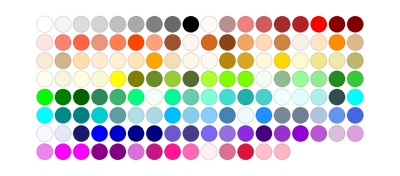

```mathematica
ColorData["HTML","Panel"]
```

```mathematica
RGBColor[0.8549019607843137, 0.6470588235294118, 0.12549019607843137]RGBColor[0.5450980392156862, 0.27058823529411763, 0.07450980392156863]RGBColor[0.27450980392156865, 0.5098039215686274, 0.7058823529411764]RGBColor[0.11764705882352941, 0.5647058823529412, 1.]RGBColor[0.2549019607843137, 0.4117647058823529, 0.8823529411764706]RGBColor[0.27450980392156865, 0.5098039215686274, 0.7058823529411764]RGBColor[0.27450980392156865, 0.5098039215686274, 0.7058823529411764]RGBColor[0.2549019607843137, 0.4117647058823529, 0.8823529411764706]
```